# Hydrogen Electron Orbit ( non - relativitic )

## Theory

### General

```mathematica
(* Hamiltonian *)
H = 1/2 P^2/m-k/r
```

```mathematica
P=-ⅈ ℏ ∇
```

```mathematica
(* Time independent Schrodinger equation *)
-ℏ^2/(2m) ∇^2 ψ+V ψ = Ε ψ
```

```mathematica
(* since V is sperical *)
V=-k/r
```

```mathematica
∇^2 =1/r^2∂/(∂r)(r^2∂/(∂r))+1/(r^2 Sin[θ])∂/(∂θ)(Sin[θ]∂/(∂θ))+1/(r^2(Sin^2)[θ])∂^2/(∂ϕ^2)
```

```mathematica
ψ = R[r]Y[θ,ϕ]
```

```mathematica
-ℏ^2/(2m) (1/r^2 ⅆ/ⅆr(r^2 ⅆR/ⅆr)Y+R/(r^2 Sin[θ])∂/(∂θ)(Sin[θ](∂Y)/(∂θ))+R/(r^2(Sin^2)[θ])(∂^2 Y)/(∂ϕ^2))+V R Y=Ε R Y
```

```mathematica
ⅆ/ⅆr(r^2 ⅆR/ⅆr)1/R+1/Sin[θ]∂/(∂θ)(Sin[θ](∂Y)/(∂θ))1/Y+1/((Sin^2)[θ])(∂^2 Y)/(∂ϕ^2)1/Y=(2m r^2)/-ℏ^2(Ε -V)
```

```mathematica
ⅆ/ⅆr(r^2 ⅆR/ⅆr)-(2m r^2)/ℏ^2(V-Ε)R=l(l+1)R (* Radial Part *)
```

```mathematica
Sin[θ]∂/(∂θ)(Sin[θ](∂Y)/(∂θ))+(∂^2 Y)/(∂ϕ^2)+l(l+1)Y (Sin^2)[θ]=0 (* Angular Part *)
```

#### other view of the Laplacian

```mathematica
∇^2 =1/r^2∂/(∂r)(r^2∂/(∂r))-1/r^2 L^2
(* where L is reduced angular mometum *)
L^2=-(1/Sin[θ]∂/(∂θ)(Sin[θ]∂/(∂θ))+1/((Sin^2)[θ])∂^2/(∂ϕ^2))
(* we can define *)
```

```mathematica
(* Recall that *)
L = r × p
Lx = -ⅈ (y ∂/(∂z)-z ∂/(∂y))
```

```mathematica
Ly=-ⅈ(z∂/(∂x)-x ∂/(∂z))
```

```mathematica
Lz = -ⅈ(x ∂/(∂y)-y ∂/(∂x))
```

```mathematica
(* the coordinate transform *)
x=r Sin[θ]Cos[ϕ];
y=r Sin[θ]Sin[ϕ];
z=r Cos[θ];
(* the Jacobian matrix is *)
({{D[x,r], D[x,θ], D[x,ϕ]}, {D[y,r], D[y,θ], D[y,ϕ]}, {D[z,r], D[z,θ], D[z,ϕ]}})
(* and the transform is the invert of this matrix *)
{{ Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]},{(Cos[θ] Cos[ϕ])/r,(Cos[θ]  Sin[ϕ])/r,-Sin[θ]/r},{-(Csc[θ] Sin[ϕ])/r,(Cos[ϕ] Csc[θ])/r,0}}
(* i.e. *)
∂/(∂x)=(∂r)/(∂x)∂/(∂r)+(∂θ)/(∂x)∂/(∂θ)+(∂ϕ)/(∂x)∂/(∂ϕ)=Cos[ϕ] Sin[θ]∂/(∂r)+(Cos[θ] Cos[ϕ])/r∂/(∂θ)-(Csc[θ] Sin[ϕ])/r∂/(∂ϕ)
```

```mathematica
∂/(∂y)=(∂r)/(∂y)∂/(∂r)+(∂θ)/(∂y)∂/(∂θ)+(∂ϕ)/(∂y)∂/(∂ϕ)=Sin[θ] Sin[ϕ]∂/(∂r)+(Cos[θ]  Sin[ϕ])/r∂/(∂θ)+(Cos[ϕ] Csc[θ])/r∂/(∂ϕ)
```

```mathematica
∂/(∂z)=(∂r)/(∂z)∂/(∂r)+(∂θ)/(∂z)∂/(∂θ)+(∂ϕ)/(∂z)∂/(∂ϕ)=Cos[θ]∂/(∂r)-Sin[θ]/r∂/(∂θ)
```

```mathematica
(* for matematica calculation a = ∂/(∂r), b = ∂/(∂θ), c = ∂/(∂ϕ) *)
Lx =r Sin[θ]Sin[ϕ] (Cos[θ]a-Sin[θ]/r b)-r Cos[θ] (Sin[θ] Sin[ϕ]a+(Cos[θ]  Sin[ϕ])/r b+(Cos[ϕ] Csc[θ])/r c)//Simplify
Ly=r Cos[θ](Cos[ϕ] Sin[θ]a+(Cos[θ] Cos[ϕ])/r b-(Csc[θ] Sin[ϕ])/r c)-r Sin[θ]Cos[ϕ](Cos[θ]a-Sin[θ]/r b)//Simplify
Lz = r Sin[θ]Cos[ϕ] (Sin[θ] Sin[ϕ]a+(Cos[θ]  Sin[ϕ])/r b+(Cos[ϕ] Csc[θ])/r c)-r Sin[θ]Sin[ϕ] (Cos[ϕ] Sin[θ]a+(Cos[θ] Cos[ϕ])/r b-(Csc[θ] Sin[ϕ])/r c)//Simplify
```

-c Cos[ϕ] Cot[θ]-b Sin[ϕ]

b Cos[ϕ]-c Cot[θ] Sin[ϕ]

c

```mathematica
Lx = -ⅈ(-Sin[ϕ]∂/(∂θ)- Cos[ϕ] Cot[θ]∂/(∂ϕ))
```

```mathematica
Ly= -ⅈ(Cos[ϕ]∂/(∂θ)-Cot[θ] Sin[ϕ]∂/(∂ϕ))
```

```mathematica
Lz=-ⅈ∂/(∂ϕ)
```

```mathematica
L^2=Lx Lx+Ly Ly+Lz Lz
=-(  -Sin[ϕ]∂/(∂θ)- Cos[ϕ] Cot[θ]∂/(∂ϕ))( -Sin[ϕ]∂/(∂θ)- Cos[ϕ] Cot[θ]∂/(∂ϕ))-(Cos[ϕ]∂/(∂θ)-Cot[θ] Sin[ϕ]∂/(∂ϕ))(Cos[ϕ]∂/(∂θ)-Cot[θ] Sin[ϕ]∂/(∂ϕ))-∂^2/(∂ϕ^2)
=Sin[ϕ]∂/(∂θ)(Sin[ϕ]∂/(∂θ))+Sin[ϕ]∂/(∂θ)(Cos[ϕ] Cot[θ]∂/(∂ϕ))+Cos[ϕ] Cot[θ]∂/(∂ϕ)(Sin[ϕ]∂/(∂θ))+Cos[ϕ] Cot[θ]∂/(∂ϕ)(Cos[ϕ] Cot[θ]∂/(∂ϕ))+Cos[ϕ]∂/(∂θ)(Cos[ϕ]∂/(∂θ))-Cos[ϕ]∂/(∂θ)(Cot[θ] Sin[ϕ]∂/(∂ϕ))-Cot[θ] Sin[ϕ]∂/(∂ϕ)(Cos[ϕ]∂/(∂θ))+Cot[θ] Sin[ϕ]∂/(∂ϕ)(Cot[θ] Sin[ϕ]∂/(∂ϕ))+∂^2/(∂ϕ^2)
```

```mathematica
=-Cot[θ]∂/(∂θ)-∂^2/(∂θ^2)-(1+(Cot^2)[θ])∂^2/(∂ϕ^2)
```

```mathematica
=-(1/Sin[θ]∂/(∂θ)(Sin[θ]∂/(∂θ))+1/((Sin^2)[θ])∂^2/(∂ϕ^2)) = L^2
```

```mathematica
(* introduce Lup and Ldn Operator *)
Lup = Collect[Lx+ⅈ Ly,{b,c}]
Ldn = Collect[Lx-ⅈ Ly,{b,c}]
```

b (ⅈ Cos[ϕ]-Sin[ϕ])+c (-Cos[ϕ] Cot[θ]-ⅈ Cot[θ] Sin[ϕ])

b (-ⅈ Cos[ϕ]-Sin[ϕ])+c (-Cos[ϕ] Cot[θ]+ⅈ Cot[θ] Sin[ϕ])

```mathematica
Lup = Exp[ⅈ ϕ]( ∂/(∂θ)+ ⅈ Cot[θ]∂/(∂ϕ))
```

```mathematica
Ldn = Exp[-ⅈ ϕ]( -∂/(∂θ)+ⅈ Cot[θ]∂/(∂ϕ))
```

```mathematica
L^2= Lz^2+1/2(Lup Ldn + Ldn Lup)
```

```mathematica
(* Set up Operator for Mathematica *)
Lsquare[Y_]:=-(1/Sin[θ] D[Sin[θ]D[Y,θ],θ]+1/((Sin^2)[θ])D[Y,{ϕ,2}])
Lx[Y_]:=-ⅈ(-Sin[ϕ]D[Y,θ]- Cos[ϕ] Cot[θ]D[Y,ϕ])
Ly[Y_]:=-ⅈ(Cos[ϕ]D[Y,θ]-Cot[θ] Sin[ϕ]D[Y,ϕ])
Lz[Y_]:=-ⅈ D[Y,ϕ]
Lup[Y_]:=Lx[Y]+ⅈ Ly[Y]//Simplify
Ldn[Y_]:=Lx[Y]-ⅈ Ly[Y]//Simplify
```

```mathematica
(* The equation *)
-ℏ^2/(2m) (1/r^2 ⅆ/ⅆr(r^2 ⅆR/ⅆr)Y-R/r^2 L^2 Y)+V R Y=Ε R Y
(* angular part *)
Lsquare[Y]=l(l+1)Y (* Angular Part *)
(* There exist a highest Level *)
Lup [Yup] = 0
(* Y = Θ Φ *)
Tan[θ] 1/Θ(∂Θ)/(∂θ)=- ⅈ 1/Φ(∂Φ)/(∂ϕ)
- ⅈ 1/Φ(∂Φ)/(∂ϕ)=m  ⇒ Φ=Exp[ⅈ m ϕ]
Tan[θ] 1/Θ(∂Θ)/(∂θ)=m  ⇒Θ = C[1](Sin^m)[θ]
```

```mathematica
Yup[m_]:=Sin[θ]^m Exp[ⅈ m ϕ];
```

```mathematica
(* Notice that the eigenvalue of Ldn is not 1 *)
```

```mathematica
(* Normalization formula *)
NY[Y_]:=√Integrate[ComplexExpand[Conjugate[Y]]ComplexExpand[Y]2π Sin[θ],{θ,0,π}]
```

```mathematica
(* Lz requir*)
Lz[ Yup ]= m Yup
```

```mathematica
Lz[Yup[m]]/Yup[m]
```

m

```mathematica
(* to find m , sub Yup in the L^2 *)
Lsquare[Yup[m]] = l(l+1)Yup[m]
```

```mathematica
Lsquare[Yup[m]]/Yup[m]//Simplify
```

m (1-m Cot[θ]^2+m/(Sin^2[θ]))

```mathematica
Refine[Solve[m(1-m Cot[θ]^2+m/Sin[θ]^2)==l(l+1),m]//Simplify,l>0]
```

{{m→1/2 (-2-2 l)},{m→l}}

```mathematica
Yq[l_,m_]:= Cos[θ]^(l-Abs[m])Sin[θ]^Abs[m] Exp[ⅈ m ϕ]
Y[l_,m_]:=Yq[l,m]/NY[Yq[l,m]]
```

```mathematica
Table[{Y[l,m],NY[Y[l,m]]},{l,0,2},{m,-l,l,1}]
```

{{{1/(2 √π),1}},{{1/2 ⅇ^(-ⅈ ϕ) √(3/(2 π)) Sin[θ],1},{1/2 √(3/π) Cos[θ],1},{1/2 ⅇ^(ⅈ ϕ) √(3/(2 π)) Sin[θ],1}},{{1/4 ⅇ^(-2 ⅈ ϕ) √(15/(2 π)) Sin[θ]^2,1},{1/2 ⅇ^(-ⅈ ϕ) √(15/(2 π)) Cos[θ] Sin[θ],1},{1/2 √(5/π) Cos[θ]^2,1},{1/2 ⅇ^(ⅈ ϕ) √(15/(2 π)) Cos[θ] Sin[θ],1},{1/4 ⅇ^(2 ⅈ ϕ) √(15/(2 π)) Sin[θ]^2,1}}}

### Angular Part

```mathematica
Y=Θ Φ
Sin[θ]∂/(∂θ)(Sin[θ](∂Θ)/(∂θ))1/Θ+l(l+1) (Sin^2)[θ]+1/Φ(∂^2 Φ)/(∂ϕ^2)=0
```

```mathematica
1/Φ(∂^2 Φ)/(∂ϕ^2)=-m^2
Φ=Exp[ⅈ m ϕ]
(* by boundary conditon (periodic)*)
m=±1,±2, ....
```

```mathematica
Sin[θ]∂/(∂θ)(Sin[θ](∂Θ)/(∂θ))+(l(l+1) (Sin^2)[θ]-m^2)Θ=0
(* The solution *)
Θ= A LegendreP[m,l,Cos[θ]]
l=0,1,2,... 
m=-l,-l+1,...,-1,0,1,...,l-1,l
```

```mathematica
(* A is normalization constant *)
ⅆ^3 r = r^2 Sin[θ] ⅆrⅆθⅆϕ
```

```mathematica
A=((-1)^m(Sign[m+0.5]+1)/2+1(1-(Sign[m+0.5]+1)/2))√((2l+1)/(4π)((l-Abs[m])!)/((1+Abs[m])!))
```

```mathematica
Y[θ_,ϕ_,l_,m_]:=((-1)^m(Sign[m+0.5]+1)/2+1(1-(Sign[m+0.5]+1)/2))√((2l+1)/(4π)((l-Abs[m])!)/((l+Abs[m])!))Exp[ⅈ m ϕ]LegendreP[l,Abs[m],Cos[θ]]
```

```mathematica
Table[Y[θ,ϕ,l,m]//Simplify,{l,1,2},{m,-l,l}]//TableForm
Table[NY[Y[θ,ϕ,l,m]],{l,1,2},{m,-l,l}]//TableForm
```

-1/2 ⅇ^(-ⅈ ϕ) √(3/(2 π)) √(Sin[θ]^2) | 1/2 √(3/π) Cos[θ] | 1/2 ⅇ^(ⅈ ϕ) √(3/(2 π)) √(Sin[θ]^2) |  | 
1/4 ⅇ^(-2 ⅈ ϕ) √(15/(2 π)) Sin[θ]^2 | -1/2 ⅇ^(-ⅈ ϕ) √(15/(2 π)) Cos[θ] √(Sin[θ]^2) | 1/8 √(5/π) (1+3 Cos[2 θ]) | 1/2 ⅇ^(ⅈ ϕ) √(15/(2 π)) Cos[θ] √(Sin[θ]^2) | 1/4 ⅇ^(2 ⅈ ϕ) √(15/(2 π)) Sin[θ]^2

1 | 1 | 1 |  | 
1 | 1 | 1 | 1 | 1

### Radial Part

```mathematica
(* Radial Part *)
ⅆ/ⅆr(r^2 ⅆR/ⅆr)-(2m r^2)/ℏ^2(V-Ε)R=l(l+1)R 
ⅆ/ⅆr(r^2 ⅆR/ⅆr)+(2m r^2)/ℏ^2(k/r+Ε)R=l(l+1)R
```

```mathematica
(* Let u[r]=r R[r]*)
 (ⅆ u)/(ⅆ r)=R[r]+ r (ⅆ R)/(ⅆ r)
 r(ⅆ u)/(ⅆ r)= u + r^2 (ⅆ R)/(ⅆ r) 
ⅆ/ⅆr(r^2 ⅆR/ⅆr)= ⅆ/ⅆr(r(ⅆ u)/(ⅆ r)- u )=r(ⅆ^2 u)/(ⅆ r^2)
```

```mathematica
r(ⅆ^2 u)/(ⅆ r^2) +(2m r)/ℏ^2(k/r+Ε)u=l(l+1)u/r
```

```mathematica
ℏ^2/(2m)(ⅆ^2 u)/(ⅆ r^2) +k/r u+Ε u=(ℏ^2 l(l+1))/(2m)u/r^2 
-ℏ^2/(2m Ε)(ⅆ^2 u)/(ⅆ r^2) +(-k/(Ε r) +(ℏ^2 l(l+1))/(2m Ε) 1/r^2)u= u
```

```mathematica
(* simplifly κ = (√(-2m Ε))/ℏ*)
1/κ^2(ⅆ^2 u)/(ⅆ r^2) +(α/(κ r) -(l(l+1))/κ^2 1/r^2)u= u 
(* ρ = κ r  *)
(ⅆ^2 u)/(ⅆ ρ^2) =(1-α/ρ +l(l+1) 1/ρ^2) u
```

```mathematica
(* ρ -> ∞ *)
(ⅆ^2 u)/(ⅆ ρ^2) =u 
u = A Exp[-ρ] (* as u has to be finite -> 0, as ρ -> ∞ *)
```

```mathematica
(* ρ -> 0 *)
(ⅆ^2 u)/(ⅆ ρ^2) =(l(l+1) 1/ρ^2) u 
u= c ρ^(l+1)
```

```mathematica
(* Combine the solution *)
u = ρ^(l+1) Exp[-ρ] v[ρ]
```

```mathematica
D[D[ ρ^(l+1) Exp[-ρ] v[ρ],ρ],ρ]//Simplify
```

ⅇ^-ρ ρ^(-1+l) ((l+l^2-2 l ρ+(-2+ρ) ρ) v[ρ]+ρ (2 (1+l-ρ) v'[ρ]+ρ v''[ρ]))

```mathematica
(* Compare *)
((l+l^2)/ρ-2 l ρ+(-2+ρ) ρ) v[ρ]+(2 (1+l-ρ) v'[ρ]+ v''[ρ])  ==(l(l+1) 1/ρ)   v[ρ]//Simplify
```

(2+2 l-ρ) ρ v[ρ]==2 (1+l-ρ) v'[ρ]+v''[ρ]

```mathematica
(* need series solution *)
```

```mathematica
R[n_,l_,a_]:=√((2/(n a))^3((n-l-1)!)/(2 n(n+l)!))Exp[-r/(n a)](2 r/(n a))^l LaguerreL[n-l-1,2l+1,2 r/(n a)]
```

```mathematica
(* Normailization condition *)
NR[R_]:=√Integrate[R^2 r^2,{r,0,∞}]
```

```mathematica
MaxR[n_,l_]:=Solve[D[R[n,l,1],r]==0,r]
```

```mathematica
MaxR[3,2]
```

{{r→0},{r→6}}

```mathematica
Table[ {R[n,l,1],NR[R[n,l,1]]},{n,1,3},{l,0,n-1}]//TableForm
```

2 ⅇ^-r
1 |  | 
(ⅇ^(-r/2) (2-r))/(2 √2)
1 | (ⅇ^(-r/2) r)/(2 √6)
1 | 
(2 ⅇ^(-r/3) (27-18 r+2 r^2))/(81 √3)
1 | 1/27 √(2/3) ⅇ^(-r/3) (4-(2 r)/3) r
1 | 2/81 √(2/15) ⅇ^(-r/3) r^2
1

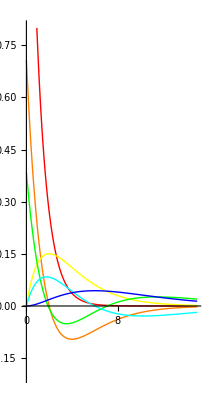

```mathematica
Plot[{{2 ⅇ^-r},{(ⅇ^(-r/2) (2-r))/(2 √2),(ⅇ^(-r/2) r)/(2 √6)},{(2 ⅇ^(-r/3) (27-18 r+2 r^2))/(81 √3),1/27 √(2/3) ⅇ^(-r/3) (4-(2 r)/3) r,2/81 √(2/15) ⅇ^(-r/3) r^2}},{r,0,15},PlotRange->{-0.2,0.8},AspectRatio->2, PlotStyle->{Red,Orange,Yellow,Green, Cyan,Blue}]
```

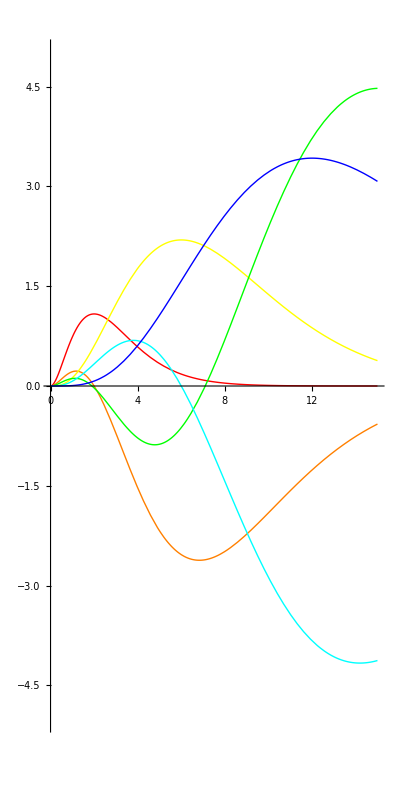

```mathematica
Plot[Evaluate[r^2{{2 ⅇ^-r},{(ⅇ^(-r/2) (2-r))/(2 √2),(ⅇ^(-r/2) r)/(2 √6)},{(2 ⅇ^(-r/3) (27-18 r+2 r^2))/(81 √3),1/27 √(2/3) ⅇ^(-r/3) (4-(2 r)/3) r,2/81 √(2/15) ⅇ^(-r/3) r^2}}],{r,0,15},PlotRange->{-5,5},AspectRatio->2, PlotStyle->{Red,Orange,Yellow,Green, Cyan,Blue}]
```

## Complete Solution

```mathematica
ψ[r_,θ_,ϕ_,n_,l_,m_,a_]:=  √((2/(n a))^3((n-l-1)!)/(2 n(n+l)!))Exp[-r/(n a)](2 r/(n a))^l LaguerreL[n-l-1,2l+1,2 r/(n a)] √((2l+1)/(4π)((l-Abs[m])!)/((l+Abs[m])!))Exp[ⅈ m ϕ]LegendreP[l,Abs[m],Cos[θ]] (* a = Bohr Radiu *)
(* Mean Radial*)
MeanR[n_,l_,m_]:=Integrate[ψ[r,θ,ϕ,n,l,m,1]r ψ[r,θ,-ϕ,n,l,m,1] r^2 Sin[θ],{r,0,∞},{θ,0,π},{ϕ,0,2π}]
(* Norm ψ sqaure *)
Normψ2[r_,θ_,ϕ_,n_,l_,m_]:=ψ[r,θ,ϕ,n,l,m,1] ψ[r,θ,-ϕ,n,l,m,1]
(* Regtangular Form *)
Regψ[x_,y_,z_,n_,l_,m_]:=Normψ2[r,θ,0,n,l,m]/.{r->√(x^2+y^2+z^2),Cos[θ]->z/(√(x^2+y^2+z^2)),Sin[θ]->(√(x^2+y^2))/(√(x^2+y^2+z^2))}//Simplify
```

```mathematica
Table[ψ[r,θ,ϕ,n,0,0,h]^2 n^3,{n,1,4}]/.r->0//Simplify
```

{1/(h^3 π),1/(h^3 π),1/(h^3 π),1/(h^3 π)}

```mathematica
Table[MeanR[n,l,0],{n,1,4},{l,0,n-1}]//TableForm
```

3/2 |  |  | 
6 | 5 |  | 
27/2 | 25/2 | 21/2 | 
24 | 23 | 21 | 18

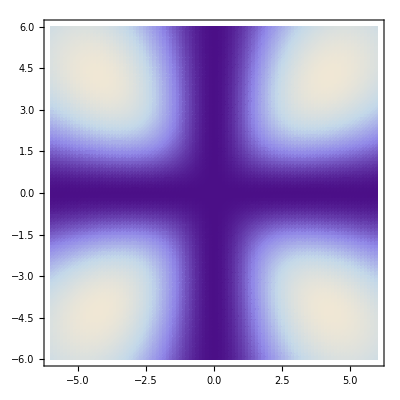

```mathematica
DensityPlot[Regψ[0,x,y,3,2,1],{x,-6,6},{y,-6,6},PlotPoints->100]
```

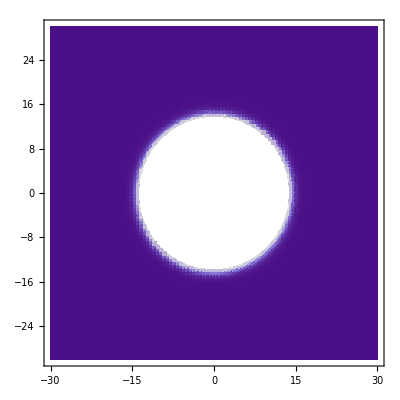
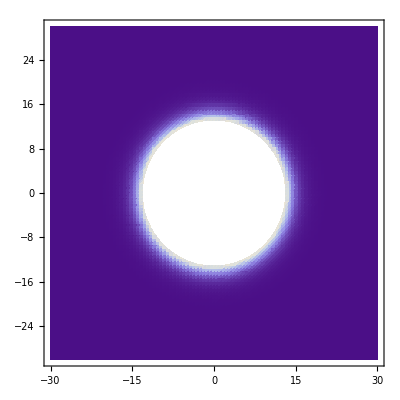
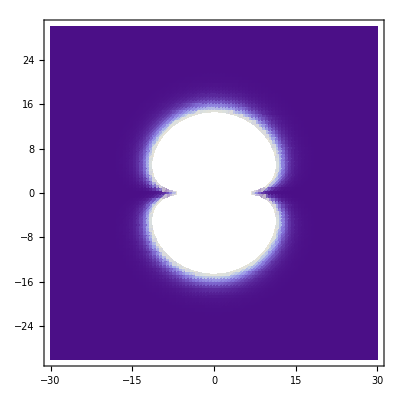
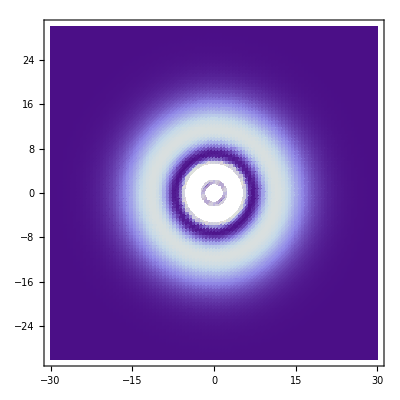
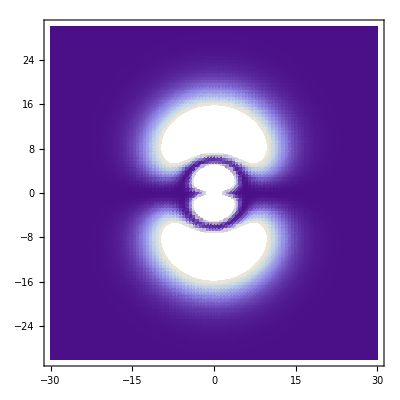
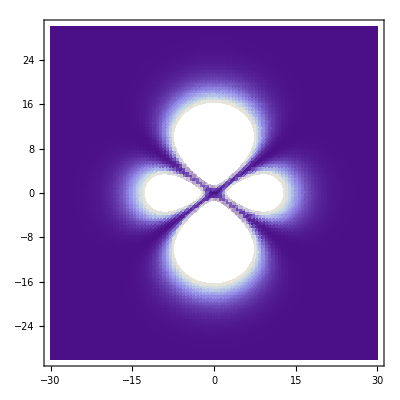
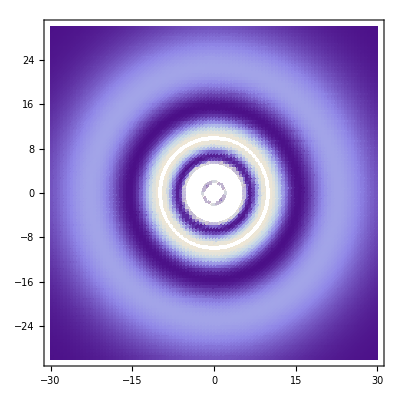
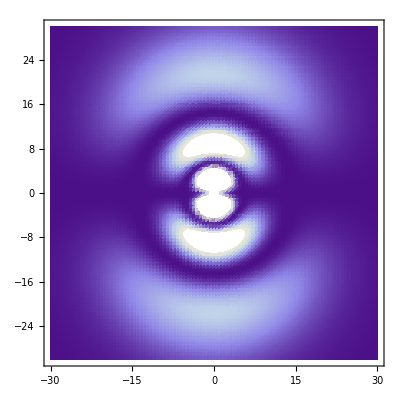
-Graphics- |  |  | 
-Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Table[DensityPlot[Regψ[0,x,y,n,l,0],{x,-30,30},{y,-30,30},PlotPoints->100],{n,1,4},{l,0,n-1}]//TableForm
```

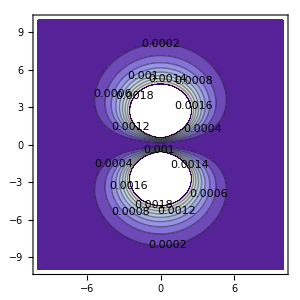
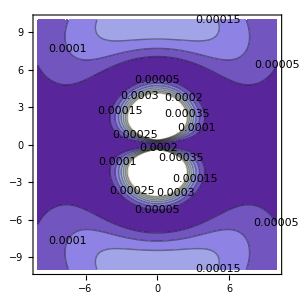
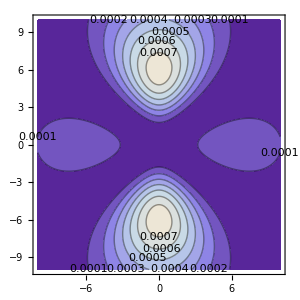
|  | 
-Graphics- |  | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
Table[ContourPlot[Regψ[0,x,y,n,l,0],{x,-10,10},{y,-10,10},PlotPoints->70,ContourLabels->True,ImageSize->300],{n,1,4},{l,0,n-1}]//TableForm
```

```mathematica
Conjugate[g+ⅈ b]
```

-ⅈ Conjugate[b]+Conjugate[g]

```mathematica
ComplexExpand[Conjugate[ψ[r,θ,0,n,l,0,h]]] 1/r ComplexExpand[ψ[r,θ,0,n,l,0,h]]//Simplify
```

1/(n^4 π r)4^l ⅇ^(-(2 r)/(h n)) √((1+2 l)^2) (r^2/(h^2 n^2))^l √(((-1-l+n)!)^2/(h^6 ((l+n)!)^2)) (Im[LaguerreL[-1-l+n,1+2 l,(2 r)/(h n)]]^2+Re[LaguerreL[-1-l+n,1+2 l,(2 r)/(h n)]]^2) (Im[LegendreP[l,Cos[θ]]]^2+Re[LegendreP[l,Cos[θ]]]^2)

```mathematica
Integrate[1/(n^4 π r)4^l ⅇ^(-(2 r)/(h n)) √((1+2 l)^2) (r^2/(h^2 n^2))^l √(((-1-l+n)!)^2/(h^6 ((l+n)!)^2)) (Im[LaguerreL[-1-l+n,1+2 l,(2 r)/(h n)]]^2+Re[LaguerreL[-1-l+n,1+2 l,(2 r)/(h n)]]^2) (Im[LegendreP[l,Cos[θ]]]^2+Re[LegendreP[l,Cos[θ]]]^2)r^2,{r,0,∞}]4π
```

$Aborted

## Complete Solution ( alternative )

```mathematica
Ψ[n_,l_,m_,a_]:= Y[l,m]R[n,l,a]
```

```mathematica
NormΨ[f_]:=√Integrate[ComplexExpand[Conjugate[f]]ComplexExpand[f] r^2 2π Sin[θ],{θ,0,π},{r,0,∞}]
```

```mathematica
Ψ[2,1,1,a]
```

1.00206×10^25 ⅇ^(-9.44863×10^9 r) r Y[1,1]

```mathematica
(* The expectation of mean radius *)
MeanRadius[f_]:= Integrate[f^2 r r^2,{r,0,∞}]
(* mean momemtum *)
MeanMom[f_]:= Integrate[f D[f,r] r^2,{r,0,∞}]
(* Mean momemtum 2 *)
MeanMom2[f_]:= Integrate[f D[f,{r,2}] r^2,{r,0,∞}]
(* Mean momemtum 4 *)
MeanMom4[f_]:= Integrate[f D[f,{r,4}] r^2,{r,0,∞}]
```

```mathematica
Table[MeanRadius[R[n,l,1]],{n,1,3},{l,0,n-1}]
```

{{3/2},{6,5},{27/2,25/2,21/2}}

```mathematica
Table[MeanMom[R[n,l,1]],{n,1,3},{l,0,n-1}]
```

{{-1},{-1/4,-1/4},{-1/9,-1/9,-1/9}}

```mathematica
Table[ Integrate[R[n,l,1]^2 1/r^3 r^2,{r,0,∞}],{n,1,3},{l,1,n-1}]
```

{{},{1/24},{1/81,1/405}}

```mathematica
Table[1/(l(l+1/2)(l+1)n^3),{n,1,3},{l,1,n-1}]
```

{{},{1/24},{1/81,1/405}}

```mathematica
Table[MeanMom4[R[n,l,1]],{n,1,3},{l,0,n-1}]
```

{{1},{-1/16,-1/16},{-5/243,-5/243,-1/1215}}

```mathematica
(* Subsitute the solution into the Hamiltiona *)
Refine[Ψ[1,0,0,a],a>0]
Refine[NormΨ[Ψ[1,0,0,a]],a>0]
```

ⅇ^(-r/a)/(a^(3/2) √π)

1

```mathematica
SpheMom[f_]:=1/r^2 D[r^2 D[f,r],r]-1/r^2 Lsquare[f]
```

```mathematica
H[f_]:=-ℏ^2/(2m)SpheMom[f]-e^2/(4 π ϵ r)f
```

```mathematica
Refine[SpheMom[Ψ[1,0,0,a]],a>0]//Simplify
```

(ⅇ^(-r/a) (-2 a+r))/(a^(7/2) √π r)

```mathematica
Integrate[Ψ[1,0,0,a]H[Ψ[1,0,0,a]] r^2 Sin[θ]2π,{r,0,∞},{θ,0,π}]
```

If[Re[a]>0,(-(a e^2)/(π ϵ)+(2 ℏ^2)/m)/(4 a^2),Integrate[-(e^2 ⅇ^(-(2 r)/a) r)/(a^3 π ϵ)+(4 ⅇ^(-(2 r)/a) r ℏ^2)/(a^4 m)-(2 ⅇ^(-(2 r)/a) r^2 ℏ^2)/(a^5 m),{r,0,∞},Assumptions→Re[a]≤0]]

```mathematica
(-(a e^2)/(π ϵ)+(2 ℏ^2)/m)/(4 a^2)/.a->(4 π ϵ ℏ^2)/(m e^2)//Simplify
```

-(e^4 m)/(32 π^2 ϵ^2 ℏ^2)

```mathematica
Y[0,0]
```

1/(2 √π)

```mathematica
R[1,0]
```

2 ⅇ^-r

## Momemtum of an electron

```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
SetCoordinates[Spherical]
```

Spherical[Rr,Ttheta,Pphi]

```mathematica
Div[Grad[ψ[Rr,Ttheta,Pphi,1,0,0,a]]]//Simplify
```

(√(1/a^3) ⅇ^(-Rr/a) (-2 a+Rr))/(a^2 √π Rr)

```mathematica
ψ[Rr,Ttheta,Pphi,1,0,0,a]
```

(√(1/a^3) ⅇ^(-Rr/a))/(√π)

```mathematica
(* P = ⅈ ℏ ∇ *)
Pmean[n_,l_,m_]:= Integrate[ Conjugate[ψ[Rr,Ttheta,Pphi,n,l,m,1]] ⅈ ℏ Grad[ψ[Rr,Ttheta,Pphi,n,l,m,1]] Rr^2 Sin[θ],{Rr,0,∞},{θ,0,π},{ϕ,0,2π}]
```

```mathematica
Pmean[1,0,0]
```

{-ⅈ ℏ,0,0}

```mathematica
KEmean[n_,l_,m_]:= Integrate[ Conjugate[ψ[Rr,Ttheta,Pphi,n,l,m,1]] (ⅈ ℏ )^2 Div[Grad[ψ[Rr,Ttheta,Pphi,n,l,m,1]]] Rr^2 Sin[θ],{Rr,0,∞},{θ,0,π},{ϕ,0,2π}]
KEmean[2,0,0]
```

ℏ^2/4

```mathematica
Integrate[(√(1/a^3) ⅇ^(-Rr/a))/(√π)(ⅈ ℏ )^2(√(1/a^3) ⅇ^(-Rr/a) (-2 a+Rr))/(a^2 √π Rr)Rr^2 Sin[θ],{Rr,0,∞},{θ,0,π},{ϕ,0,2π},Assumptions->Re[a]>0 ]
```

ℏ^2/a^2

```mathematica
(* the speed of the ground state *)
Solve[1/(2m)ℏ^2/a^2== (1/(√(1-β^2))-1)m  c^2,β]//Simplify
```

{{β→-0.00729721},{β→0.00729721}}

```mathematica
1/137//N
```

0.00729927

```mathematica
ℏ=6.626068×10^-34/(2π)(* m^2 kg/s *);
m=9.10938188×10^-31 (* kg *);
e = 1.60217646×10^-19 ;
ϵ=8.854187817×10^-12 (* F / m *);
a = (4 π ϵ ℏ^2)/(m e^2);
c=299792458;
```

```mathematica
α = e^2/(4 π ϵ) 1/(ℏ c)
```

0.00729735

```mathematica
Clear[a,ϵ,e, m,ℏ,c]
```

## Transition Rate

```mathematica
Fermi Golden Rule State that the transition Rate
TR = (2π)/ℏ Norm[<f|H|i>] ρ
f = final state
i = initial state
ρ=density of final state
```

$Aborted